```mathematica
EVENDEGREE[g_?ConnectedGraphQ]:=Module[{oddVertices,shortestPathGroups},oddVertices=Select[VertexList[g],OddQ[VertexDegree[g,#]]&];GraphSum[g,Graph@FindIndependentEdgeSet@Subgraph[g,oddVertices]]]
```

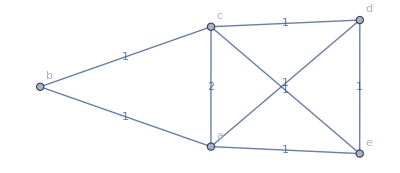

```mathematica
G=Graph[{a,b,c,d,e},{a<->b,a<->e,a<->d,a<->c,b<->c,c<->e,c<->d,d<->e},VertexLabels->Automatic,EdgeWeight->Thread[{a<->b,a<->e,a<->d,a<->c,b<->c,c<->e,c<->d,d<->e}->{1,1,1,2,1,1,1,1}],EdgeLabels->"EdgeWeight"]
```

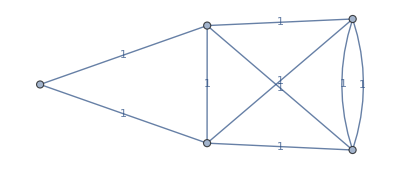

```mathematica
Graph[EVENDEGREE@G,EdgeLabels->"EdgeWeight"]
```


GraphSum[-Graphics-,-Graphics-]

```mathematica
GraphSum[G,Graph@FindIndependentEdgeSet@Subgraph[G,EVENDEGREE@G]]
```

```mathematica
EulerianGraphQ[GraphSum[G,Graph@FindIndependentEdgeSet@Subgraph[G,EVENDEGREE@G]]]
```

True

```mathematica
FindEulerianCycle[EVENDEGREE[G]]
```

{{a<->e,e<->d,d<->c,c<->e,e<->b,b<->d,d<->a,a<->c,c<->b,b<->a}}

```mathematica
MultiSet[g_?ConnectedGraphQ]:=Module[{undirectededges},Cases[EdgeList[g],_UndirectedEdge]]
```

```mathematica
MultiSet[G]
```

{}

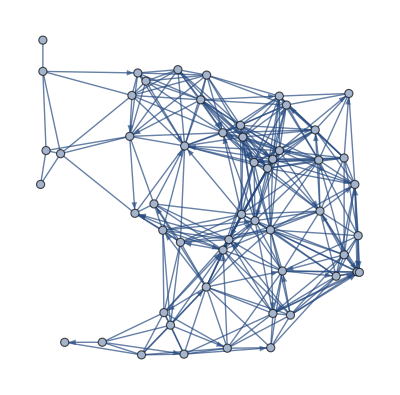

```mathematica
𝒢=MixedGraph[RandomGraph[SpatialGraphDistribution[54,.3]],.2]
```

```mathematica
(VertexInDegree[𝒢,#]-VertexOutDegree[𝒢,#])&/@VertexList[𝒢]
```

{-1,-1,-1,-2,-3,-3,-1,0,-3,0,-3,-2,-5,-1,-1,0,-3,0,-1,2,-2,0,-1,0,-1,1,-1,1,-3,0,2,1,0,2,1,1,1,1,2,1,1,2,2,3,2,1,2,2,1,0,4,0,0,3}

```mathematica
FindMinimumCostFlow[𝒢,(VertexInDegree[𝒢,#]-VertexOutDegree[𝒢,#])&/@VertexList[𝒢],"OptimumFlowData"]
```

OptimumFlowData[…]

```mathematica
MultiSet[g_?ConnectedGraphQ]:=Module[{undirectedEdges,firstToLast,lastToFirst},undirectedEdges=Select[EdgeList[g],Head[#]==UndirectedEdge&];firstToLast=Graph[Fold[EdgeAdd[#1,DirectedEdge[First[#2],Last[#2]]]&,g,undirectedEdges],EdgeWeight->Join[Values[AssociationMap[AnnotationValue[{g,#},EdgeWeight]&,undirectedEdges]],AnnotationValue[{g,#},EdgeWeight]&/@EdgeList[g]]];lastToFirst=Graph[Fold[EdgeAdd[#1,DirectedEdge[Last[#2],First[#2]]]&,firstToLast,undirectedEdges],EdgeWeight->Join[Values[AssociationMap[AnnotationValue[{firstToLast,#},EdgeWeight]&,undirectedEdges]],AnnotationValue[{firstToLast,#},EdgeWeight]&/@EdgeList[firstToLast]]];Graph[Fold[EdgeAdd[#1,UndirectedEdge[Last[#2],First[#2]]]&,lastToFirst,undirectedEdges],EdgeWeight->Join[Values[AssociationMap[AnnotationValue[{lastToFirst,#},EdgeWeight]&,undirectedEdges]],AnnotationValue[{lastToFirst,#},EdgeWeight]&/@EdgeList[lastToFirst]],EdgeCapacity->Join[ConstantArray[∞,3EdgeCount[g]],ConstantArray[2,EdgeCount[g]]]]]
```

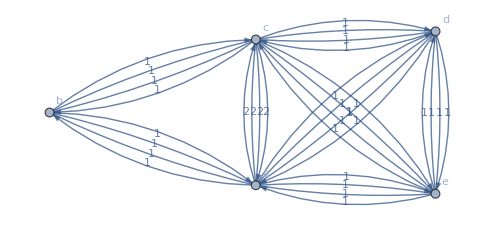

```mathematica
MultiSet[G]
```

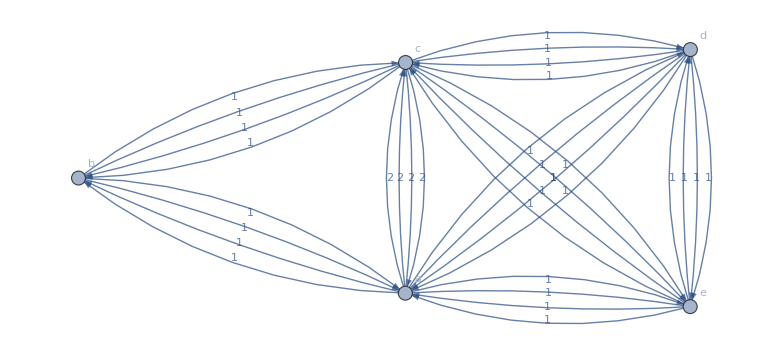

```mathematica
𝒢=MixedGraph[MultiSet[G],.4]
```

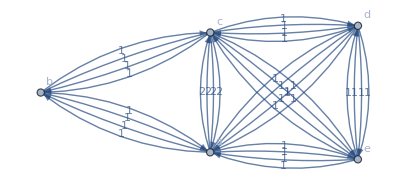
FindMinimumCostFlow[-Graphics-,{1,1,0,-1,-1},OptimumFlowData]

```mathematica
FindMinimumCostFlow[𝒢,(VertexInDegree[𝒢,#]-VertexOutDegree[𝒢,#])&/@VertexList[𝒢],"OptimumFlowData"]
```

```mathematica
PrintDefinitions["FindMinimumCostFlow"]
```

FindEulerianCycle::ngen: The generalized FindEulerianCycle[Graph[<5>, <32>]] is not implemented.

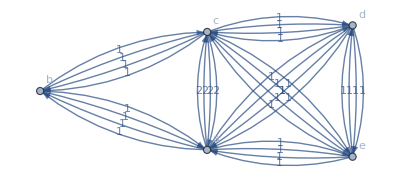
FindEulerianCycle[-Graphics-]

```mathematica
FindEulerianCycle[𝒢]
```